```mathematica
d = Daljica[{-1, 1}, {3, -1}]
```

```mathematica
ClearAll[Dolzina]
Dolzina[Daljica[AA_,BB_]]:= Norm[AA-BB]
```

```mathematica
Dolzina[Daljica[{-1, 1}, {3, -1}]]
```

2 √5

Global`Dolzina

Dolzina[Daljica[{-1,1},{3,-1}]]:=Norm[AA-BB]
 
Dolzina[Daljica[AA_,BB_]]:=Norm[AA-BB]

```mathematica
Slika[Daljica[AA_, BB_]]:=Line[{AA, BB}]
Slika[d]
```

Line[{{-1,1},{3,-1}}]

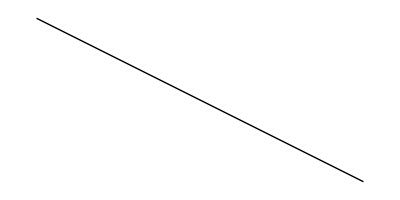

```mathematica
Narisi[d_] := Graphics[Slika[d]]
Narisi[d]
```

```mathematica
EnacbaNosilke[Daljica [AA_, BB_]] := Module[{x1,y1, x2, y2, n, k},
{x1, y1} = AA;
{x2, y2} = BB;
k = (y2-y1) / (x2-x1);
n= n/.First[Solve[y1 == k*x1 +n, n]]; 
y == k*x+n
]

EnacbaNosilke[d]
```

y==1/2-x/2

```mathematica
d = Daljica[{-1, 1}, {3, -1}]
```

Daljica[{-1,1},{3,-1}]

```mathematica
dd=Daljica[{11, 1}, {44, 17}]
```

Daljica[{11,1},{44,17}]

```mathematica
Presek[Daljica[AA_, BB_], Daljica[CC_, DD_]] :=Module[{a, b},
a = EnacbaNosilke[d];
b = EnacbaNosilke[dd];
resitev =Solve[a && b, {x,y}]]

Presek[d,dd]
```

{{x→319/65,y→-127/65}}

```mathematica
m1 = Mnogokotnik [{0,0}, {1,1}, {0,3}, {-1,2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
Slika[Mnogokotnik[t__]] := Map[Line, m1]
Narisi[t__] := Graphics[Slika[t]]
Narisi[t]
```

-Graphics-